15.4 Polar Integration Example

We want to integrate the function z=(x^2+y^2)^(3/2)over the region D between the polar functions r=cos(θ) and r=(√2)/2. There are many ways to do the integral. I think the simplest is to use the symmetry of the region, and of the function (x^2+y^2)^(3/2), and just integrate over the top half, i.e. the red and purple parts:

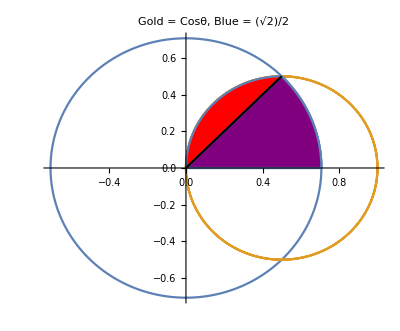

```mathematica
Show[PolarPlot[{Sqrt[2]/2,Cos[t]},{t,-π,π}],RegionPlot[Sqrt[x^2+y^2]<Sqrt[2]/2&&Sqrt[x^2+y^2]<x/Sqrt[x^2+y^2],{x,0,1},{y,0,1},PlotStyle->{Red}],RegionPlot[Sqrt[x^2+y^2]<Sqrt[2]/2&&Sqrt[x^2+y^2]<x/Sqrt[x^2+y^2]&&x>y,{x,0,1},{y,0,1},PlotStyle->{Purple}],Plot[x,{x,0,1/2},PlotStyle->{Black}],PlotLabel->RawBoxes[RowBox[{RowBox[{"Gold"," ","="," ","Cosθ"}],","," ",RowBox[{"Blue"," ","="," ",FractionBox[SqrtBox["2"],"2"]}]}]],LabelStyle->{GrayLevel[0]}]
```

To do so, we split into two integrals in polar coordinates, to the left and right of the black line. The black line is at angle π/4. The purple region is bounded by the radial curves r=0,r=(√2)/2, while the red region is bounded by the radial curves r=0,r=cosθ. So we get 

∫∫_D (x^2+y^2)^(3/2)dA=2((∫_0)^(π/4)∫_0^(√2/2) r^3 r dr dθ+∫_(π/4)^(π/2) ∫_0^Cosθ r^3 r dr dθ)=16/75-43/(150 √2)+π/(40 √2)≈.066165.

Evaluating this integral comes down to the substitution u=sinθ, as we saw in class. 

Another way would be to integrate over the interior of gold circle r=cosθ, and subtract the integral over the green region (as below):

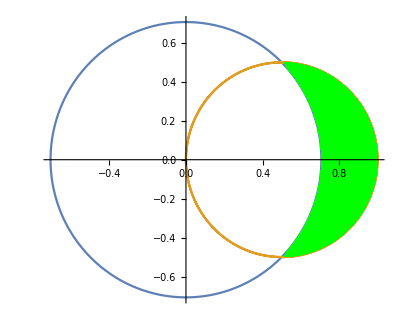

```mathematica
Show[PolarPlot[{Sqrt[2]/2,Cos[t]},{t,-π,π}],RegionPlot[Sqrt[x^2+y^2]>Sqrt[2]/2&&Sqrt[x^2+y^2]<x/Sqrt[x^2+y^2],{x,0,1},{y,-1,1},PlotStyle->{Green},BoundaryStyle->None]]
```

This integral looks like: 

∫∫_D (x^2+y^2)^(3/2)dA=2∫_0^(π/2) ∫_0^Cosθ r^3 r dr dθ-∫_(-π/4)^(π/4) ∫_(√2/2)^Cosθ r^3 r dr dθ ≈.066165.

Note that I’ve used the symmetry of the function z=r^3, and of the region, to do the first integral. 

Yet another way would be to integrate over the right half of the blue circle r=(√2)/2, and subtract the integral over the pink part (as below):

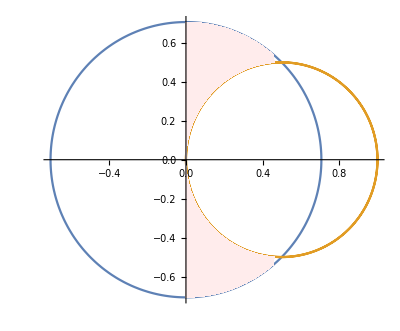

```mathematica
Show[PolarPlot[{Sqrt[2]/2,Cos[t]},{t,-π,π}],RegionPlot[Sqrt[x^2+y^2]<Sqrt[2]/2&&Sqrt[x^2+y^2]>x/Sqrt[x^2+y^2],{x,0,1},{y,-1,1},PlotStyle->{LightPink},BoundaryStyle->None]]
```

This would give the integral 

∫∫_D (x^2+y^2)^(3/2)dA=∫_(-π/2)^(π/2) ∫_0^(√2/2) r^3 r dr dθ-2∫_(π/4)^(π/2) ∫_Cosθ^(√2/2) r^3 r dr dθ≈.066165.